# 22.06 Liquid Metal Cooled Fast Reactor Project

## Warner McGhee, Lead thermal hydraulics and safety

## Our initial specifications

Power output: 100 MWth
Fuel type: 20% enriched UO_2
Fuel geometry:
	- Square array of cylindrical fuel rods, circular outline.
	- Fuel diameter: 0.01 m
	- Rod outer diameter: 0.0113 m
	- Active rod length: 1.0 m
	- Pitch: 0.0135 m

## Using the ELSY as an approximation for power density

Source: https://www.iaea.org/NuclearPower/Downloadable/Meetings/2012/2012-02-29-03-02-TM-FR/11a_Tarantino-Cinotti.pdf

```mathematica
(* Given in documentation *)
Q=1500*^6; (* Wth *)
numAssemblies=162;
rodsPerAssembly=428;
numRods=numAssemblies*rodsPerAssembly;
L=0.9; (* m, active fuel length *)
d=0.0105; (* m, fuel diameter *)
p=0.0139; (* m, pitch, square *)
Tin=400+273.15; (* K *)
Tout=480+273.15; (* K *)
```

Properties of lead
Source: https://www.oecd-nea.org/science/reports/2007/pdf/chapter2.pdf, page 89

```mathematica
(*
cp[T_]:=175.1-4.961*^-2*T+1.985*^-5*T^2-2.099*^-9*T^3-1.524*^6*T^-2; (* J/(kg*K) *)
ρ[T_]:=11367-1.1944*T; (* kg/m^3 *)
μ[T_]:=4.55*^-4*Exp[1069/T]; (* Pa*s *);
k[T_]:=9.2+0.011*T; (* W/(m*K) *)
*)
(*
cpLBE[T_] := 159-2.72*10^-2*T+7.12*10^-6*T^2;
ρLBE[T_] :=11096-1.3236*T;
μLBE[T_] := 4.94*10^-4*Exp[754.1/T];
kLBE[T_] := 3.61+1.517*10^-2*T-1.741*10^-6*T^2;
*)
(* Uncomment to use LBE *)
cp[T_] := 159-2.72*10^-2*T+7.12*10^-6*T^2;
ρ[T_] :=11096-1.3236*T;
μ[T_] := 4.94*10^-4*Exp[754.1/T];
k[T_] := 3.61+1.517*10^-2*T-1.741*10^-6*T^2;
```

```mathematica
(* Calculations *)
massFlow=Q/(cp[Tout]*(Tout-Tin)); (* kg/s *)
A=numRods*(p^2-Pi*d^2/4);
vb=massFlow/(A*ρ[Tout]) (* m/s *)
```

1.76175

```mathematica
Vfuel=numRods*L*Pi*d^2/4; (* m^3 *)
q′′′fuel=Q/Vfuel (* W/m^3 *)
```

2.77601×10^8

## Applying power density and limits from ELSY to our specifications

```mathematica
(* Specifications *)
Q=100*^6; (* Wth *)
L=1.0; (* m, active fuel length *)
df=0.01; (* m, fuel pellet diameter *)
d=0.0113; (* m, fuel rod outer diameter *)
p=0.0135; (* m, pitch, square *)
Tin=400+273.15; (* K *)
Tout=550+273.15; (* K *)
```

```mathematica
(* Calculations *)
Vfuel=Q/q′′′fuel; (* m^3 *)
numFuelRods=Vfuel/(L*Pi*df^2/4)
```

4586.58

Based on our core geometry, the number of total rods (control + fuel) is 4/3 the number of fuel rods.

```mathematica
numRods=(4/3)*numFuelRods;
massFlow=Q/(cp[Tout]*(Tout-Tin)); (* kg/s *)
A=numRods*(p^2-Pi*df^2/4);
vb=massFlow/(A*ρ[Tout]) (* m/s *)
```

0.742716

I fudged around with the temperature until I got the bulk velocity of the lead to be similar to that of the ELSY. The higher temperature of the lead could cause corrosion. LFR research in Sweden has tested FeCrAl alloys in lead up to 550 °C for 2 years with no significant corrosion or degradation, but the lifetime of some components may be such that we do have material failures. We should wither reconsider the core geometry or do more research to see if this temperature is too high.

## Calculating pressure drop and necessary core height

Using problem 9.6 from the textbook as a basis, here is the pressure drop in the core:

```mathematica
(* From Table 9.6 in Textbook: *)
a=0.1339;
b1=0.09059;
b2=-0.09926;

(* Entrance and Exit *)
Achannel=p^2-Pi*d^2/4; (* m^2 *)
dh=4*Achannel/(Pi*d); (* m *)
ReD=ρ[Tin]*vb*dh/μ[Tin];
f=0.184*ReD^-0.2;


ΔPentrance=0.5*ρ[Tin]*vb^2/2; (* Pa *)
ΔPexit=ρ[Tin]*vb^2/2; (* Pa *)


(* Friction *)
C′=a+b1*(p/d-1)+b2*(p/d-1)^2;
Re′=ρ[Tin]*vb*dh/μ[Tin];
f2=C′/(Re′^0.18);
ΔPfriction=f2*ρ[Tin]*L*vb^2/(2*dh); (* Pa *)

(* Spacers (3), using Rehme model *)
As=(p^2-(p-0.001)^2); (* m^2 *) 
Av=p^2-(Pi*d^2)/4;(* m^2 *) 
Cv=6.5; (* From graph in textbook *)
ΔPspacers=3*Cv*(ρ[Tin]*vb^2*As^2)/(2*Av^2); (* Pa *)


(* Fittings (2), using Rehme model *)
As=(p^2-(p-0.0015)^2); (* m^2 *) 
Av=p^2-(Pi*d^2)/4; (* m^2 *) 
ΔPfittings=2*Cv*(ρ[Tin]*vb^2*As^2)/(2*Av^2); (* Pa *)
ΔPtotal=ΔPspacers+ΔPfriction+ΔPentrance+ΔPexit
```

16260.1

Here is the required vessel height to overcome the pressure drop using natural convection:

```mathematica
g=9.8; (* m/s^2 *)
h=ΔPtotal/(g*(ρ[Tin]-ρ[Tout])) (* m *)
```

8.35695

```mathematica
massFlow
```

4713.6

## Calculating maximum temperatures

From my literature review, the power shape is a cosine function and my conservative estimate of peaking factor is 1.4 x 1.3 ~ 2.

```mathematica
peakingFactor =2;

Rfo=df/2;(*m*)
tgap=0.00015;
Rci=(df/2)+tgap;(*m*)
Rco=d/2;(*m*)
kclad=16;(*W/(m*K)*)
hgap=5200;(*W/(m^2*K)*)
kuo2=3;(*W/(m*K)*)
P=0.05;
α2=1.5;

(*Calculations*)
Rgap=(Rfo+Rci)/2;(*m*)
kfuel=(1-P)/(1+(α2-1)*P)*kuo2;(*W/(m*K)*)
q′max=(peakingFactor*Q)/(numRods*L);(*W/m^3*)
q′′ave=Q/(numRods*L*2*Pi*Rco);(*W/m^2*)
q′′max=peakingFactor*q′′ave;(*W/m^2*)
q′′′max=(peakingFactor*Q)/(numRods*L*Pi*Rfo^2);(*W/m^3*)
perim=Pi*d;(*m,wetted perimeter of channel*)
PrandtlNum=cp[Tout]*μ[Tout]/k[Tout];
NusseltNum=0.023*ReD^0.8*PrandtlNum^0.4;
h=NusseltNum*k[Tout]/dh;

Rthfuel=1/(4*Pi*kfuel);(*m*K/W*)
Rthgap=1/(2*Pi*Rgap*hgap);(*m*K/W*)
Rthclad=Log[Rco/Rci]/(2*Pi*kclad);(*m*K/W*)
Rthflow=1/(2*Pi*Rco*h);(*m*K/W*)
ΣR=Rthfuel+Rthgap+Rthclad+Rthflow;
Tcenter[z_]:=ΣR*q′max*Sin[(Pi*z)/L]+Tin+(Tout-Tin)/2*(1-Cos[(Pi*z)/L]);
dTcenter[z_]:=ΣR*q′max*Cos[(Pi*z)/L]*Pi/L+(Tout-Tin)/2*Sin[(Pi*z)/L]*Pi/L;
```

```mathematica
Solve[0==dTcenter[z], z]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{z→-0.479975},{z→0.520025}}

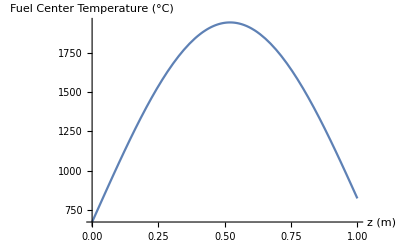

```mathematica
Plot[Tcenter[x],{x,0,L},AxesLabel->{"z (m)", "Fuel Center Temperature (°C)"}]
```

```mathematica
Print["The maximum fuel temperautre is ",Tcenter[0.5199883],"°C"]
```

The maximum fuel temperautre is 1941.12°C

```mathematica
90*p
```

1.215